## Exponential approximations derivations for stars and gas

By Davi Rodrigues & Alejandro Hernandez-Arboleda
This file is part of the NAVanalysis code
July, 2022

```mathematica
isBurkertWithGaussianPriors = True;
SetDirectory @ NotebookDirectory[];
Needs @ "NAVbaseCode`";

SetDirectory @ FileNameJoin[{NotebookDirectory[], "Output"}];
```

## Stellar contribution

```mathematica
Clear[vExp, fitExpVdisk, fitExpVdiskPlot, chi2, associationFitExpVdisk];

(*
  vExp comes from Binney & Tremaine 2nd Ed., eq.(2.165). 
  It is assumed that  Σ = Subscript[Σ, 0] ⅇ^(-R/h), where Subscript[Σ, 0] has dimension of mass/length^2, it  is the surface mass density.
*)
vExp[R_,logSigma0_,h_]= Block[{y}, 
  y = R/(2 h);
  kpc Sqrt[4 π G0 10^logSigma0 h y^2 (BesselI[0,y] BesselK[0,y] - BesselI[1,y] BesselK[1,y])]
];

chi2[model_List, dataObs_List, uncertainty_List] := chi2[model, dataObs, uncertainty]  = Total[(model-dataObs)^2/uncertainty^2];

associationFitExpVdisk::usage="associationFitExpVdisk[data(R x Vdisk)] fits the radial vs disk velocity curve data as a rotation curve for an exponential disk and returns an association with several data. "<>
  "For fitting, it is assumed an uncertainty of 10% on the velocity. The important point is not the porportionality constant, but that the uncertainty is proportional to the velocity. "<>
  "If data = {},  associationFitExpVdisk returns {}.";

associationFitExpVdisk[dataRVdisk_List] := fitExpVdisk[dataRVdisk] = Block[
  {sol, R, h, bestLogSigma0, besth, logSigma0, listModel, uncertainty, rMax, solExtended},
  If[
    dataRVdisk=={}, 
    Return[{}]
  ];
  rMax = Last @ dataRVdisk[[All, 1]];
  listModel = vExp[# , logSigma0, h] & /@ dataRVdisk[[All,1]];
  uncertainty = Max[{0.10 dataRVdisk[[#, 2]], 2}] & /@ Range @ Length @ dataRVdisk; (*Assumes uncertainty of 10% or 2 km/s. *)
  sol = NMinimize[
    {chi2[listModel, dataRVdisk[[All, 2]], uncertainty], h > 0, logSigma0 > 1},
    {{logSigma0, 6, 10}, {h, 0.5, 10}},
    Method-> Automatic
  ];
  (*{logSigma0, h, Chi2, Number of data points }*)
  solExtended = {First @ sol, First @ sol/(Length[dataRVdisk] - 2), logSigma0, h, h/rMax, rMax, Length[dataRVdisk]} /. Last@sol;
  AssociationThread[{"Chi2", "Chi2red", "logSigma0", "h", "hn", "rMax", "dataPoints"}, solExtended]
];

plotFittedExpVdisk[dataRVdisk_List, bestVdiskValues_List]:= Block[
  {vMax, bestLogSigma0, besth, rMax},
  If[
    dataRVdisk=={}, 
    Return[{}]
  ];
  {bestLogSigma0, besth} = bestVdiskValues;
  vMax = Max @ dataRVdisk[[All, 2]];
  rMax = Last @ dataRVdisk[[All, 1]];
  Show[
    {
      ListPlot[
        dataRVdisk,
        PlotRange -> {{0, 1.1 * rMax}, {0, 1.1 * vMax}}
      ],
      Plot[vExp[R, bestLogSigma0, besth], {R, 0, 100}, PlotRange -> All]
    }
  ]
];
```

```mathematica
Echo["Computing datasetExpVdiskNoBulge. This takes some seconds."];
datasetExpVdiskNoBulge = Dataset[
  DeleteCases[ 
    associationFitExpVdisk[gdRBulgeless[{Rad, Vdisk}, #]] & /@ Range[175], 
  {}]
] // EchoTiming
```

Computing datasetExpVdiskNoBulge. This takes some seconds.

45.5341

```mathematica
Export["headerAux.txt", {
  "# Additional velocity distribution: a fast sample analysis for dark matter or modified gravity models",
  "# by A. Hernandez-Arboleda, D. C. Rodrigues, A. Wojnar",
  "# ",
  "# The complete Table B1 data: the best fit results of an exponential model for the stellar component of 122 SPARC galaxies.",
  "# First column: best-fit disk scale length (h).",
  "# Second column: best-fit central surface brightness (logSigma0).",
  "# Third column: normalized disk scale length (hn).",
  "# Fourth column: the minimum chi-squared value (Chi2).",
  "# Fifth column: the number of galaxy data points that were used for the fit (dataPoints).", 
  "# ",
  "# "
}];

datasetStarsExport = datasetExpVdiskNoBulge[All,{"h","logSigma0", "hn","Chi2", "dataPoints"}];
Export["StellarExponentialBestFitAux.tsv", datasetStarsExport, Alignment-> Left, "TextDelimiters"->None];

Run["cat headerAux.txt StellarExponentialBestFitAux.tsv > StellarExponentialBestFit.tsv"]; (*It is only guaranteed to work in Unix systems. Sorry Windows...*)

DeleteFile["headerAux.txt"];
DeleteFile["StellarExponentialBestFitAux.tsv"];

Export["datasetExpVdiskNoBulge.m", datasetExpVdiskNoBulge];
```

### III.1.1. The hn distribution

1σ limits:  {0.0629196,0.293442}

2σ limits:  {0.0299119,0.474179}

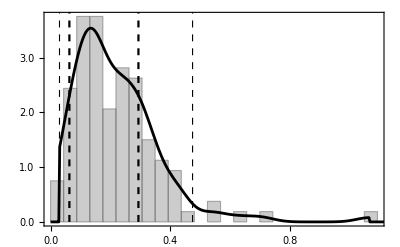

```mathematica
listhn= Normal @ datasetExpVdiskNoBulge[All, "hn"];

dist = SmoothKernelDistribution[
  listhn,
  silvermanBw @ listhn,
  MaxExtraBandwidths -> 0,
  InterpolationPoints -> 10^4 (*This is a large number, it has no relevant impact on speed *)
];

listHDPDFlimits = FindHDPDFValues[dist, oneAndTwoSigma];

list2PointsXPDF = {dist["InterpolationPoints"], dist["PDFValues"]}ᵀ;
positionMaxPDF = First @ Last @ SortBy[list2PointsXPDF, Last];

rootsSigma[i_] := (FindRoot[
  PDF[dist, x] == listHDPDFlimits[[i]], 
  #, 
  MaxIterations -> 1000
] & /@ {{x, 0, positionMaxPDF}, {x, positionMaxPDF, 1}}) ~ Quiet ~ FindRoot::brmp;

{hnLow[1], hnHigh @ 1} = x /. rootsSigma[1];
{hnLow[2], hnHigh @ 2} = x /. rootsSigma[2];

Clear @ lines;
lines[nSigmas_] := {
  Dashed,
  Thickness[0.004 / nSigmas],
  Line @ {{hnLow @ nSigmas, 0}, {hnLow @ nSigmas, 100}},
  Line @ {{hnHigh @ nSigmas, 0}, {hnHigh @ nSigmas, 100}}
};

Echo[{hnLow @ 1, hnHigh @ 1} ,"1σ limits:"];
Echo[{hnLow @ 2, hnHigh @ 2} ,"2σ limits:"];

Show[
  {
    Histogram[listhn,
      {silvermanBw @ listhn},
      "PDF", histoOptions, Epilog -> {lines @ 1, lines @ 2},
      PlotRange -> All
    ],
    nPlot[PDF[dist, x], {x, 0, 10}]
  }
]
```

## Gas contribution

```mathematica
(*
hGas is the h value for the gas distribution.
hGasn is the hn value for the gas distribution.
frho is the ratio between the gas to stellar central density.
fh is the ratio between hn and hGasn.
*)
```

#### logSigma0gas e hGasn

```mathematica
Clear[associationFitExpVgas];
associationFitExpVgas[dataRVgas_List] := associationFitExpVgas[dataRVgas] = Block[
  {sol, R, h, bestLogSigma0, besth, logSigma0, listModel, uncertainty, rMax, solExtended},
  If[
    dataRVgas=={}, 
    Return[{}]
  ];
  rMax = Last @ dataRVgas[[All, 1]];
  listModel = vExp[# , logSigma0, h] & /@ dataRVgas[[All,1]];
  uncertainty = Max[{0.10 dataRVgas[[#, 2]], 2}] & /@ Range@Length@dataRVgas; (*Max[10%, 2 km/s] uncertainty, inspired on distance error together with a minimum one.*)
  sol = NMinimize[
    {chi2[listModel, dataRVgas[[All, 2]], uncertainty], 100 rMax > h > 0.1, logSigma0 > 0.5},
    {{logSigma0, 3, 10}, {h, 3, 30}},
    Method-> Automatic
  ];
  (*{logSigma0, h, Chi2, Number of data points }*)
  solExtended = {First@sol, First@sol/(Length[dataRVgas] - 2), logSigma0, h, h/rMax, rMax, Length[dataRVgas]} /. Last@sol;
  AssociationThread[{"Chi2", "Chi2red", "logSigma0Gas", "hGas", "hGasn", "rMax", "dataPoints"}, solExtended]
];
```

```mathematica
Echo["Computing datasetExpVgasNoBulge. This takes some seconds."];
datasetExpVgasNoBulge = Dataset[
  DeleteCases[ 
    associationFitExpVgas[gdRBulgeless[{Rad, Vgas}, #]] & /@ Range[175], 
  {}]
] // EchoTiming
```

Computing datasetExpVgasNoBulge. This takes some seconds.

56.9435

```mathematica
Export["headerGasAux.txt", {
  "# Additional velocity distribution: a fast sample analysis for dark matter or modified gravity models",
  "# by A. Hernandez-Arboleda, D. C. Rodrigues, A. Wojnar",
  "# ",
  "# This file: Best fit results of an exponential model for the gaseous component of 122 SPARC galaxies.",
  "# First column: best-fit disk scale length (hGas).",
  "# Second column: best-fit central surface brightness (logSigma0Gas).",
  "# Third column: normalized disk scale length (hGasn).",
  "# Fourth column: the minimum chi-squared value (Chi2).",
  "# Fifth column: the number of galaxy data points that were used for the fit (dataPoints).", 
  "# ",
  "# "
}];

datasetGasExport = datasetExpVgasNoBulge[All,{"hGas","logSigma0Gas", "hGasn","Chi2", "dataPoints"}];
Export["GasExponentialBestFitAux.tsv", datasetGasExport, Alignment-> Left, "TextDelimiters"->None];

Run["cat headerGasAux.txt GasExponentialBestFitAux.tsv > GasExponentialBestFit.tsv"]; (*It is only guaranteed to work in Unix systems. Sorry Windows...*)

DeleteFile["headerGasAux.txt"];
DeleteFile["GasExponentialBestFitAux.tsv"];

Export["datasetExpVgasNoBulge.m", datasetExpVgasNoBulge];
```